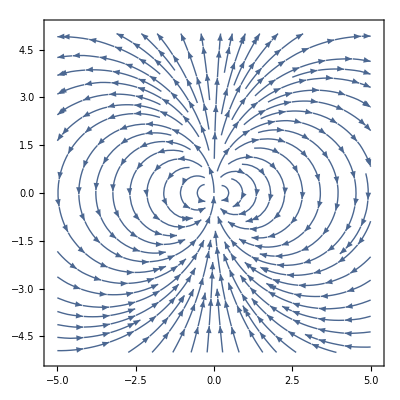

```mathematica
f1[x_,y_]:=2*x*y
g1[x_,y_]:=y^2-x^2
StreamPlot[{f1[x,y], g1[x,y]}, {x,-5,5}, {y,-5,5}]
```

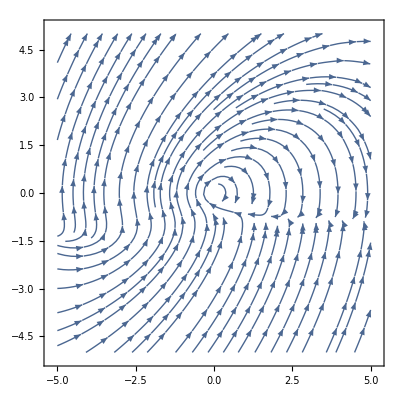

```mathematica
f2[x_,y_]:=y+y^2
g2[x_,y_]:=-x+1/5*y-x*y+6/5*y^2
StreamPlot[{f2[x,y], g2[x,y]}, {x,-5,5}, {y,-5,5}]
```

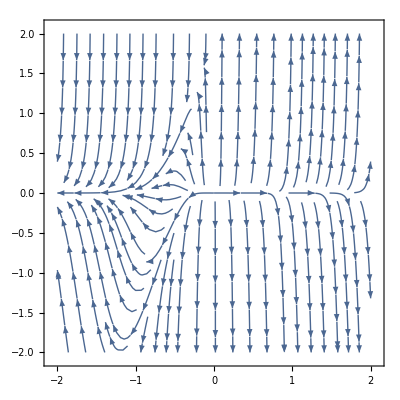

```mathematica
F1[x_,y_]:=0.3x-0.1x*y
G1[x_,y_]:=3y*(1-y/2)+5x*y
StreamPlot[{F1[x,y], G1[x,y]}, {x,-2,2}, {y,-2,2}]
```

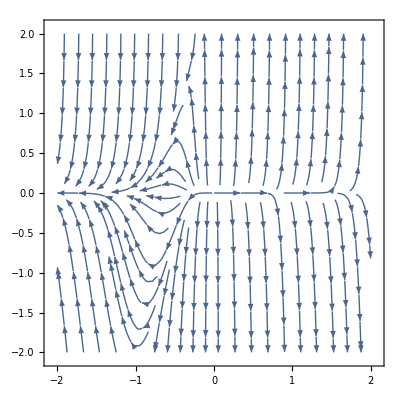

```mathematica
F2[x_,y_]:=0.3x-0.1x*y
G2[x_,y_]:=3y*(1-y/3)+5x*y
StreamPlot[{F2[x,y], G2[x,y]}, {x,-2,2}, {y,-2,2}]
```

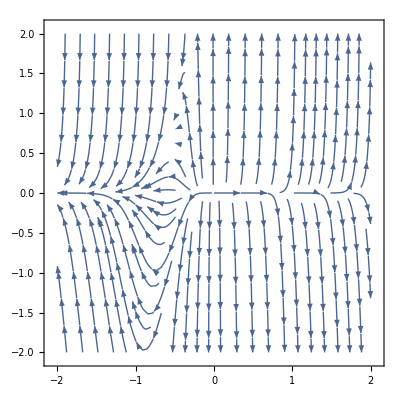

```mathematica
F3[x_,y_]:=0.3x-0.1x*y
G3[x_,y_]:=3y*(1-y/4)+5x*y
StreamPlot[{F3[x,y], G3[x,y]}, {x,-2,2}, {y,-2,2}]
```

```mathematica
n=20
F[x_,y_]:=-x*y
Y[x_,y_]:=2x*y-(n-1)*y
sol = NDSolve[{x'[t]==F[x[t],y[t]], y'[t]==Y[x[t],y[t]], x[0]==n-1, y[0]==1}, {x,y}, {t,1000}]
x[1000]/.sol
```

20

{{x→InterpolatingFunction[{{0., 1000.}}, <>],y→InterpolatingFunction[{{0., 1000.}}, <>]}}

{3.54176}

```mathematica
n=20
NSolve[2*n-1-2x+(n-1) *Log[x/(n-1)]==0, x]
```

20

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→3.54176},{x→19.9758}}